# Assignment 8

Karim Sobh
201700836

```mathematica
Problem 1
```

```mathematica
Problem 2
```

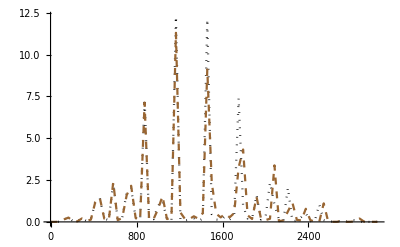

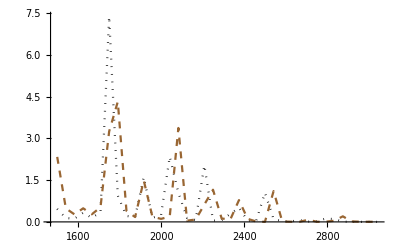

```mathematica
Clear["Global`*"]

c=300.0;
x0=0.45;
k=1000;
dx=0.004;
len=1.0;
tf=0.024;
dt=dx/(4c);
xlist= Range[0,len,dx]; iMax= Length[xlist];
nMax = 7000;
r = c * dt/dx;
m=len/dx; 
ϵ={1*10^(-5),2*10^(-5)};
style= {{Dotted, Black}, {Dashed, Brown}};
pp1= {};(*first plot*)
pp2={};(**second plot*)
locX=0.05;
locIn=NearestTo[locX][xlist->"Index"][[1]];
For[t=1,t≤2,t++, 
c1= (2-2 r^2-6 ϵ[[t]] r^2 m^2);
c2=r^2(1+ 4 ϵ[[t]] m^2);
c3= ϵ[[t]] r^2 m^2;
yt=0 Range[nMax]; 
ylist= Table[0,3, iMax];
ylist[[1]] = Exp[-k (xlist-x0)^2];
ylist[[2]] = ylist[[1]];
ylist[[All,1]]=0; ylist[[All,-1]]=0;	
For[ n=1,
n ≤ nMax, n++,
For[i=2, i < iMax, i++,
If[i ≠ 2 && i ≠ iMax-1, uu= (ylist[[2,i+2]] + ylist[[2,i-2]])];
If[i==2, uu=(ylist[[2,4]] - ylist[[2,2]])];
If[i==iMax-1, uu= (-ylist[[2,iMax-1]] + ylist[[2,iMax-3]])];
ylist[[3,i]]= c1 ylist[[2,i]] - ylist[[1,i]]+ c2 (ylist[[2,i+1]] +ylist[[2,i-1]]) - c3 uu
];
yt[[n]]=ylist[[3,locIn]];
ylist[[1]]= ylist[[2]];
ylist[[2]]= ylist[[3]];
];
p=Abs[Fourier[yt]]^2;
flist= (Range[nMax]-1)/(tf);
graphmid=NearestTo[1500][flist->"Index"][[1]];
pspec= Transpose@{flist,p};
AppendTo[pp1,ListLinePlot[pspec[[;;2 graphmid]], PlotStyle->style[[t]],PlotRange->All]];
AppendTo[pp2,ListLinePlot[pspec[[graphmid;;2 graphmid]], PlotStyle->style[[t]],PlotRange->All]];
]

Show[pp1]
Show[pp2]
```

```mathematica
Problem 3
```

```mathematica
Clear["Global`*"]

c=330.0; 
l=0.62; 
x0=0.45*len; 
f=262; 
k=2Pi f/c; 
dx=0.004; 
tf=0.02; 
dt=dx/(4c);
xlist= Range[0,l,dx]; iMax= Length[xlist];
nMax = 6000;
r = c * dt/dx; 
m=l/dx; 
ϵ=3.8*10^(-5); 
b=0.5;

c0= 1+ 2 b dt;
c1= (2-2 r^2-6 ϵ r^2 m^2 + 2 b dt);
c2=r^2(1+ 4 ϵ m^2);
c3= ϵ r^2 m^2;

ylist= Table[0,3, iMax];
ylist[[1]] = Exp[-k (xlist-x0)^2];
ylist[[2]] = ylist[[1]];
ylist[[All,1]]=0;
ylist[[All,-1]]=0;

yt=0 Range[nMax]; 
locX=0.05 l;
locIn=NearestTo[locX][xlist->"Index"][[1]];
For[ n=1,
n ≤ nMax, n++,
For[i=2, i < iMax, i++,
If[i ≠ 2 && i ≠ iMax-1, uu= (ylist[[2,i+2]] + ylist[[2,i-2]])];
If[i==2, uu=(ylist[[2,4]] - ylist[[2,2]])];
If[i==iMax-1, uu= (-ylist[[2,iMax-1]] + ylist[[2,iMax-3]])];
ylist[[3,i]]= (1/c0)(c1 ylist[[2,i]] - ylist[[1,i]]+ c2 (ylist[[2,i+1]] +ylist[[2,i-1]])- c3 uu)
];
yt[[n]]=ylist[[3,locIn]];
ylist[[1]]= ylist[[2]];
ylist[[2]]= ylist[[3]];
];
posdata= Transpose@{Range[nMax],yt};
ListLinePlot[posdata,PlotRange->All]
```

$Aborted